2

{176.,293.,385.5,389.5,390.5}

(0.+176. q^2 | 2. | 0. | 0. | 0.
2. | 206.576+293. (-1+q)^2 | 2. | 0. | 0.
0. | 2. | 635.549+385.5 (-2+q)^2 | 2. | 0.
0. | 0. | 2. | 1303.34+389.5 (-3+q)^2 | 2.
0. | 0. | 0. | 2. | 2294.94+390.5 (-4+q)^2)

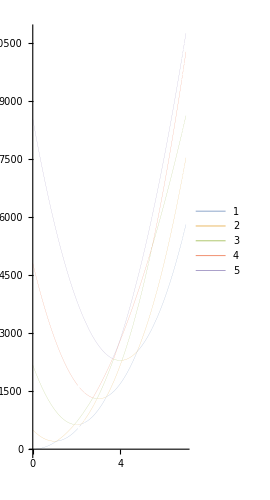

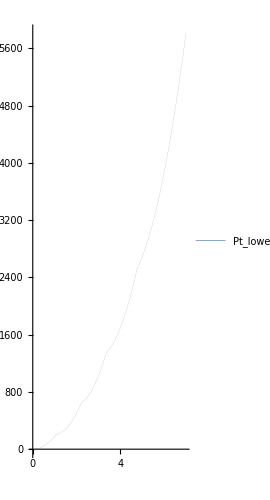

```mathematica
(*The energy landscape*)
ClearAll["Global`*"]
eneQ[q_,q0_]:=(q-q0)^2;
eneK[k_]:=0.5*k
Q0={0,01,02,03,4};
V={0,206.576,635.549,1303.336,2294.939};
K0={352,586,771,779,781};
c=2

selfQ=eneQ[q,#]&/@Q0;
selfK=eneK[#]&/@K0
EneMat=DiagonalMatrix[selfQ]* DiagonalMatrix[selfK];
overlap={c,c,c,c};
Overlap1=DiagonalMatrix[overlap,1];
Overlap2=DiagonalMatrix[overlap,-1];
Vmat=DiagonalMatrix[V];
EneMatFinal=EneMat+Overlap1+Overlap2+Vmat;
EneMatFinal//MatrixForm
values=Eigenvalues[EneMatFinal];
lowest = Min[values];

Plot[{values[[1]],values[[2]],values[[3]],values[[4]],values[[5]]},{q,0,7},PlotRange->Full,AspectRatio->Full,PlotLegends->{"1","2","3","4","5"},PlotStyle->Thickness[0]]
Plot[{lowest},{q,0,7},PlotRange->Full,AspectRatio->Full,PlotLegends->{"Pt_lowest","Ref"},PlotStyle->Thickness[0]]
```

```mathematica
values
```

{166. q^2,166. (3.77449-2.5 q+1. q^2),166. (1.97873-1.7 q+1. q^2),166. (0.780677-0.82 q+1. q^2),166. (0.261609-0.5 q+1. q^2)}

2

(422. q^2 | 2. | 0.
2. | -141+265. (1+q)^2 | 2.
0. | 2. | 603+334.5 (2+q)^2)

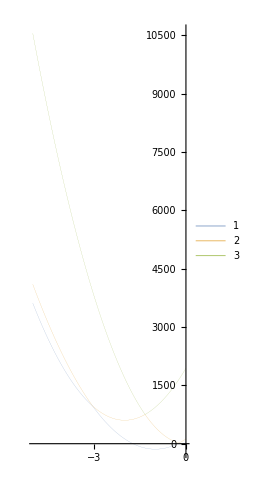

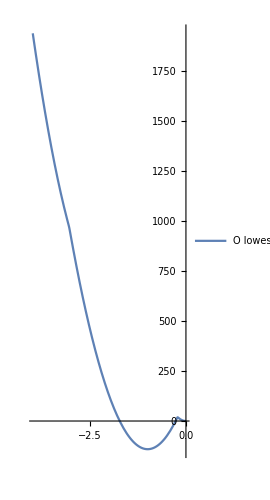

```mathematica
QO={0,-1,-2};
VO={0,-141,603};
KO={844,530,669};
cO=2
selfQO=eneQ[q,#]&/@QO;
selfKO=eneK[#]&/@KO;
EneMatO=DiagonalMatrix[selfQO]*DiagonalMatrix[selfKO];
overlapO={cO,cO};
Overlap1O=DiagonalMatrix[overlapO,1];
Overlap2O=DiagonalMatrix[overlapO,-1];
VmatO=DiagonalMatrix[VO];
EneMatFinalO=EneMatO+Overlap1O+Overlap2O+VmatO;
EneMatFinalO//MatrixForm
valuesO=Eigenvalues[EneMatFinalO];
lowestO= Min[valuesO];

Plot[{valuesO[[1]],valuesO[[2]],valuesO[[3]]},{q,0,-5},PlotRange->Full,AspectRatio->Full,PlotLegends->{"1","2","3","4","5"},PlotStyle->Thickness[0]]
Plot[{lowestO},{q,-4,0},PlotRange->Full,AspectRatio->Full,PlotLegends->{"O lowest","Ref"}]
```

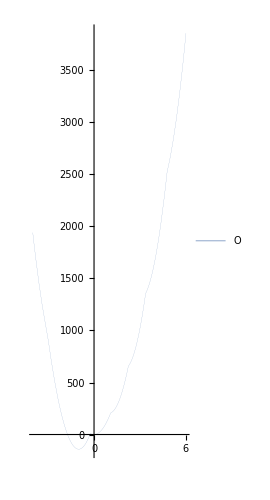

```mathematica
Plot[Min[{lowestO,lowest}],{q,-4,6},PlotRange->Full,AspectRatio->Full,PlotLegends->{"O"},PlotStyle->Thickness[.0]]
```